```mathematica
ClearAll["Global`*"]
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
data = Import[NotebookDirectory[]<>"SpherePlaneResistance.txt","Table"];
ξdata=data[[All,1]];
XAdata=data[[All,2]];
YAdata=data[[All,3]];
YBdata=data[[All,4]];
XCdata=data[[All,5]];
YCdata=data[[All,6]];
δ=0.01;
YAVal=Interpolation[Transpose[{ξdata,YAdata}]][δ];
YBVal=Interpolation[Transpose[{ξdata,YBdata}]][δ];
YCVal=Interpolation[Transpose[{ξdata,YCdata}]][δ];
XAVal=Interpolation[Transpose[{ξdata,XAdata}]][δ];
XCVal=Interpolation[Transpose[{ξdata,XCdata}]][δ];
AA={{YAVal,0,0},{0,YAVal,0},{0,0,XAVal}};
BB={{0,YBVal,0},{-YBVal,0,0},{0,0,0}};
CC={{YCVal,0,0},{0,YCVal,0},{0,0,XCVal}};
Resistance=ArrayFlatten[ {{AA,Transpose[BB]},{BB,CC}}];
```

```mathematica
TrigReduce[Cos[0.3 t] Sin[0.03 t]]
```

1/2 (-Sin[(0.27+0. ⅈ) t]+Sin[(0.33+0. ⅈ) t])

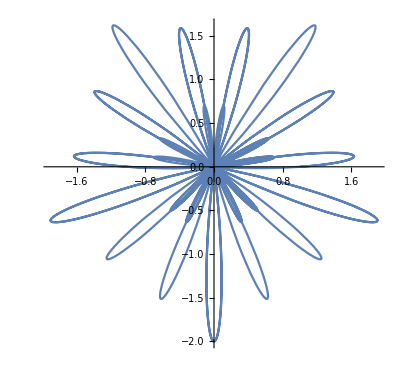

```mathematica
ParametricPlot[{(Cos[0.2 t ]+Sin[0.3 t]) Cos[0.02t],(Cos[0.2 t ]+Sin[0.3 t]) Sin[0.02 t] },{t,0,500}]
```

```mathematica
B[{ωA1_,ωA2_,A1_,A2_,ωB1_,ωB2_,B1_, B2_,ω4_},t_]:={(B1 Cos[t ωB1 ]+B2*Cos[ωB2 t ])*Sin[ω4 t],(B1 Cos[t ωB1 ]+B2*Cos[ωB1 t ])*Cos[ω4 t], (A1 Sin[t ωA1 ]+A2*Sin[ωA2 t ])}.RotationMatrix[10 Degree ,{0,1,0}];

Bflat[{ωA1_,ωA2_,A1_,A2_,ωB1_,ωB2_,B1_, B2_,ω4_},t_]:={(B1 Cos[t ωB1 ]+B2*Cos[ωB2 t ])*Sin[ω4 t],(B1 Cos[t ωB1 ]+B2*Cos[ωB1 t ])*Cos[ω4 t], (A1 Sin[t ωA1 ]+A2*Sin[ωA2 t ])};
```

```mathematica
roller[{ωA1_,ωA2_,A1_,A2_,ωB1_,ωB2_,B1_, B2_,ω4_}]:=Module[{parameter,tMax,Rq,mq,Lq,F,FLq,UΩq,Uq,Ωq,Q,quaternionRate,
q,ϕ,θ,ψ,qIC,para,sol,data,dct,tdata},
parameter={ωA1,ωA2,A1,A2,ωB1,ωB2,B1, B2,ω4};
tMax = (*Min[200 2 π/parameter[[1]],50000.0]*0+*)5000;
(*first field is magnetic , second is gravity*)

Rq={{q0^2+q1^2-q2^2-q3^2,2q1 q2+2q0 q3,2q1 q3-2q0 q2},
{2q1 q2-2q0 q3,q0^2-q1^2+q2^2-q3^2,2q2 q3+2q0 q1},
{2 q1 q3+2 q0 q2,2q2 q3-2 q0 q1, q0^2-q1^2-q2^2+q3^2}};
(*magnetic moment*)
mq=Simplify[Transpose[Rq] .{0,0,1}   ];
Lq=Simplify[Cross[mq,B[parameter,t    ]   ]];
(*force *)
F ={0 ,0,0};
FLq=ArrayFlatten[{F,Lq},1];
UΩq=Simplify[Inverse[Resistance].FLq];
Uq=UΩq[[1;;3]];
Ωq=UΩq[[4;;6]];
Q ={{q0 ,-q1,-q2,-q3},
{q1,q0,q3,-q2},
{q2,-q3,q0,q1},
{q3,q2,-q1,q0}};
(*equation 156*)
quaternionRate=1/2 Q.ArrayFlatten[{{0},Ωq},1];
q={Cos[ϕ/2]Cos[θ/2]Cos[ψ/2]-Sin[ϕ/2]Cos[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Cos[ψ/2]+Sin[ϕ/2]Sin[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Sin[ψ/2]-Sin[ϕ/2]Sin[θ/2]Cos[ψ/2],
Cos[ϕ/2]Cos[θ/2]Sin[ψ/2]+Sin[ϕ/2]Cos[θ/2]Cos[ψ/2]};
qIC = q/.{ϕ->RandomReal[2 π],θ->RandomReal[2 π],ψ->RandomReal[2 π]};
para={q0->q0[t],q1->q1[t],q2->q2[t],q3->q3[t]};
sol=NDSolve[{
q0'[t]==(quaternionRate[[1]]/.para),
q1'[t]==(quaternionRate[[2]]/.para),
q2'[t]==(quaternionRate[[3]]/.para),
q3'[t]==(quaternionRate[[4]]/.para),
x'[t]==(Uq[[1]]/.para),
y'[t]==(Uq[[2]]/.para),
q0[0]==qIC[[1]],
q1[0]==qIC[[2]],
q2[0]==qIC[[3]],
q3[0]==qIC[[4]],
x[0]==0,
y[0]==0},
{q0[t],q1[t],q2[t],q3[t],x[t],y[t]},{t,0,tMax}];
(*data=Table[x[t]/.sol[[1]],{t,0,4000,1}];
dct=FourierDCT[data];
  tdata=FourierDCT[PadRight[Take[dct,2],4000,0],3];*)
(*Mean[D[y[t]/.sol[[1]],t]/.t->Table[i,{i,tMax 0.5,tMax}]]*)
(*y[t]/.sol[[1]]/.t->Table[i,{i,200 2 π/ω1 0.5,200 2 π/ω1 0.75,1}];
200 2 π/ω1 0.75*)
(*data1=Table[{t/(  2 π/ω2),x[t]/.sol[[1]]},{t,0,4000,1}];
data2=Table[{t/(2 π /ω2),y[t]/.sol[[1]]},{t,0,4000,1}];
lm1=LinearModelFit[MovingAverage[data1,Round[      2 π/ω2]],x,x];
lm2=LinearModelFit[MovingAverage[data2,Round[      2 π/ω2]],x,x];
{sol,lm1["BestFitParameters"][[2]],lm2["BestFitParameters"][[2]]}*)
sol
]
rollerflat[{ωA1_,ωA2_,A1_,A2_,ωB1_,ωB2_,B1_, B2_,ω4_}]:=Module[{parameter,tMax,Rq,mq,Lq,F,FLq,UΩq,Uq,Ωq,Q,quaternionRate,
q,ϕ,θ,ψ,qIC,para,sol,data,dct,tdata},
parameter={ωA1,ωA2,A1,A2,ωB1,ωB2,B1, B2,ω4};
tMax =(* Min[200 2 π/parameter[[1]],50000.0]+*)5000;
(*first field is magnetic , second is gravity*)

Rq={{q0^2+q1^2-q2^2-q3^2,2q1 q2+2q0 q3,2q1 q3-2q0 q2},
{2q1 q2-2q0 q3,q0^2-q1^2+q2^2-q3^2,2q2 q3+2q0 q1},
{2 q1 q3+2 q0 q2,2q2 q3-2 q0 q1, q0^2-q1^2-q2^2+q3^2}};
(*magnetic moment*)
mq=Simplify[Transpose[Rq] .{0,0,1}   ];
Lq=Simplify[Cross[mq,Bflat[parameter,t    ]   ]];
(*force *)
F ={0 ,0,0};
FLq=ArrayFlatten[{F,Lq},1];
UΩq=Simplify[Inverse[Resistance].FLq];
Uq=UΩq[[1;;3]];
Ωq=UΩq[[4;;6]];
Q ={{q0 ,-q1,-q2,-q3},
{q1,q0,q3,-q2},
{q2,-q3,q0,q1},
{q3,q2,-q1,q0}};
(*equation 156*)
quaternionRate=1/2 Q.ArrayFlatten[{{0},Ωq},1];
q={Cos[ϕ/2]Cos[θ/2]Cos[ψ/2]-Sin[ϕ/2]Cos[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Cos[ψ/2]+Sin[ϕ/2]Sin[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Sin[ψ/2]-Sin[ϕ/2]Sin[θ/2]Cos[ψ/2],
Cos[ϕ/2]Cos[θ/2]Sin[ψ/2]+Sin[ϕ/2]Cos[θ/2]Cos[ψ/2]};
qIC = q/.{ϕ->RandomReal[2 π],θ->RandomReal[2 π],ψ->RandomReal[2 π]};
para={q0->q0[t],q1->q1[t],q2->q2[t],q3->q3[t]};
sol=NDSolve[{
q0'[t]==(quaternionRate[[1]]/.para),
q1'[t]==(quaternionRate[[2]]/.para),
q2'[t]==(quaternionRate[[3]]/.para),
q3'[t]==(quaternionRate[[4]]/.para),
x'[t]==(Uq[[1]]/.para),
y'[t]==(Uq[[2]]/.para),
q0[0]==qIC[[1]],
q1[0]==qIC[[2]],
q2[0]==qIC[[3]],
q3[0]==qIC[[4]],
x[0]==0,
y[0]==0},
{q0[t],q1[t],q2[t],q3[t],x[t],y[t]},{t,0,tMax}];
(*data=Table[x[t]/.sol[[1]],{t,0,4000,1}];
dct=FourierDCT[data];
  tdata=FourierDCT[PadRight[Take[dct,2],4000,0],3];*)
(*Mean[D[y[t]/.sol[[1]],t]/.t->Table[i,{i,tMax 0.5,tMax}]]*)
(*y[t]/.sol[[1]]/.t->Table[i,{i,200 2 π/ω1 0.5,200 2 π/ω1 0.75,1}];
200 2 π/ω1 0.75*)
(*data1=Table[{t/(  2 π/ω2),x[t]/.sol[[1]]},{t,0,4000,1}];
data2=Table[{t/(2 π /ω2),y[t]/.sol[[1]]},{t,0,4000,1}];
lm1=LinearModelFit[MovingAverage[data1,Round[      2 π/ω2]],x,x];
lm2=LinearModelFit[MovingAverage[data2,Round[      2 π/ω2]],x,x];
{sol,lm1["BestFitParameters"][[2]],lm2["BestFitParameters"][[2]]}*)
sol
]


(*B[{ω1_,ω2_,ω3_,ω4_,A1_,A2_,A3_,B1_, B2_},t_]*)
```

```mathematica
can={};
For [i=0,i<1000,
ωA1=RandomReal[{0.1,0.4}];
ωA2=RandomReal[{ω1,1}];
A1=RandomReal[{-2,2}];
A2=RandomReal[{-2,2}];
ωB1=RandomReal[{0.1,0.4}];
ωB2=RandomReal[{ωB1,1}];
B1=RandomReal[{-2,2}];
B2=RandomReal[{-2,2}];
ω4=ω1/RandomReal[{10,30}];
sol1=roller[{ωA1,ωA2,A1,A2,ωB1,ωB2,B1, B2,ω4}];
sol2=rollerflat[{ωA1,ωA2,A1,A2,ωB1,ωB2,B1,B2,ω4}];
bias=Table[x[t]/.sol1[[1]],{t,1,5000}];
flat=Table[x[t]/.sol2[[1]],{t,1,5000}];
If[(Min[flat]-Min[bias]>2)&&(Abs[Min[bias]/(y[t]/.sol1[[1]]/.t->Ordering[bias,1][[1]])]>0.36), can =Append[can,{ω1,ω2,ω4,A1,A2,B1, B2}]];
i++
]
```

```mathematica
can
```

{{0.22726,0.256303,0.00831169,0.479514,0.676842,0.391214,-1.57206},{0.22726,0.256303,0.00868876,-0.0327403,-1.29245,0.355414,1.21395},{0.22726,0.256303,0.00774876,-0.092893,1.54468,-0.815375,-1.94586},{0.22726,0.256303,0.0110635,0.000599808,0.94714,-0.457796,1.26795},{0.22726,0.256303,0.00767726,-0.192067,-0.303495,-1.15257,-1.42588},{0.22726,0.256303,0.010474,1.32145,0.0323587,1.56491,1.26162},{0.22726,0.256303,0.0211241,1.37124,-1.07427,0.837626,-1.42577}}

```mathematica
Length[can]
```

38

12.8481

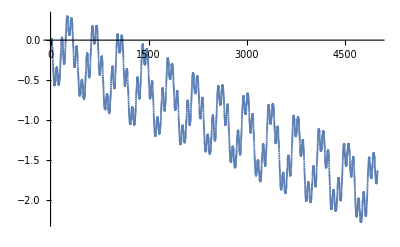

{s,s}

```mathematica
ListPlot[flat]
```

```mathematica
Export["can.csv",can]
```

can.csv

```mathematica
(*B[{ω1_,ω2_,ω3_,ω4_,A1_,A2_,A3_,B1_, B2_},t_]*)
```

{0.22726,0.256303,0.0211241,1.37124,-1.07427,0.837626,-1.42577}

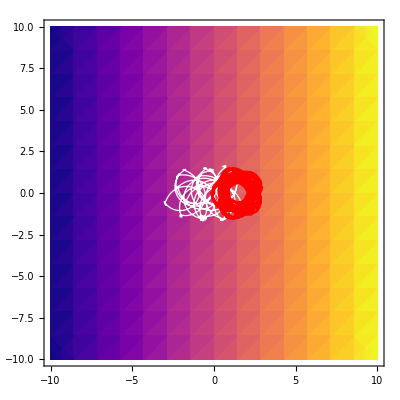

```mathematica
para=can[[7]]
sol1=roller[para];
sol2=rollerflat[para];
Show[DensityPlot[x,{x,-10,10},{y,-10,10},ColorFunction->MPLColorMap["Plasma"]],
ParametricPlot[{x[t]/.sol1[[1]],y[t]/.sol1[[1]]},{t,0,5000},PlotStyle->{White, AbsoluteThickness[0.9]},PlotRange->{{-10,10},{-10,10}},Frame->True,Axes->False],
ParametricPlot[{x[t]/.sol2[[1]],y[t]/.sol2[[1]]},{t,0,5000},PlotStyle->{Red, AbsoluteThickness[2]},PlotRange->{{-10,10},{-10,10}},Frame->True,Axes->False]

]
```

```mathematica
{0.2679972583973589,0.5207125690863094,0.009622757877744557,-0.5787506448836499,1.876592127269726,1.6544837575159823,0.22190537332375282}
```

{0.267997,0.520713,0.00962276,-0.578751,1.87659,1.65448,0.221905}

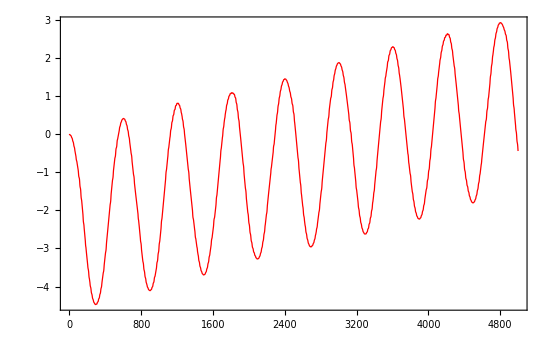

```mathematica
Plot[x[t]/.sol1[[1]],{t,0,5000},PlotStyle->{Red, AbsoluteThickness[0.9]},Frame->True,Axes->False]
```

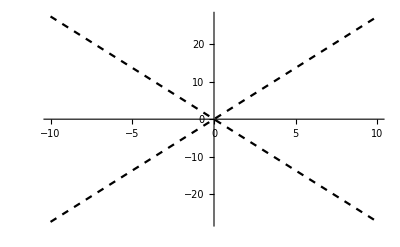

```mathematica
Plot[{Cot[20 Degree]x,-Cot[20 Degree]x},{x,-10,10},PlotStyle->{{Dashed,Black},{Dashed,Black}}]
```

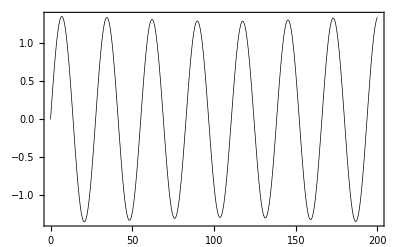

```mathematica
zfield[{ω1_,ω2_,A1_,A2_},t_]:=A1 Sin[ω1 t ]+A2 Sin[ω2 t ]
Plot[zfield[Pick[para,{1,1,0,1,1,0,0},1],t],{t,0,200},Frame->True,PlotStyle->{Black, AbsoluteThickness[0.5]}]
```

```mathematica
{0.511610972251507,0.7908980392500011,0.9721937181040985,0.018303814988236116,-0.27558310463922453,0.007526608200789653,0.06897963832795106,-1.1096269873188795,-1.4979572111557324}


{0.22872562558307657,0.6043588891674827,1.7043856680115557,0.01324038768746723,-0.5900082271963392,1.6908331541215453,-0.3248939705669116,1.2352178961027764,1.6531395301189313}
```

```mathematica
Pick[can[[2]],{1,1,1,0,1,1,1,0,0},1]
```

{0.114839,0.547198,0.704085,-0.317738,0.0414221,0.144293}

{0.114839,0.547198,0.704085}

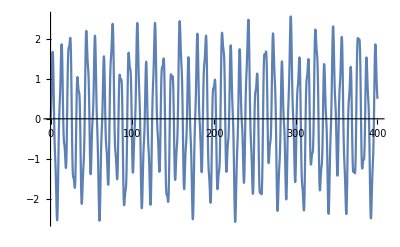

```mathematica
can[[2]][[1;;3]]
```

```mathematica
522/97.0
```

5.38144

```mathematica
{ 0.5Cos[0.18 t]+0.5 Cos[0.22 t],0, 0.2 Sin[0.2 t]}.RotationMatrix[10.0 Degree ,{0,1,0}]
```

{0.+0.984808 (0.5 Cos[0.18 t]+0.5 Cos[0.22 t])-0.0347296 Sin[0.2 t],0.,0.+0.173648 (0.5 Cos[0.18 t]+0.5 Cos[0.22 t])+0.196962 Sin[0.2 t]}

{0.+0.984808 (0.5 Cos[0.1 t]+0.5 Cos[0.2 t])-0.173648 Sin[0.2 t],0.,0.+0.173648 (0.5 Cos[0.1 t]+0.5 Cos[0.2 t])+0.984808 Sin[0.2 t]}

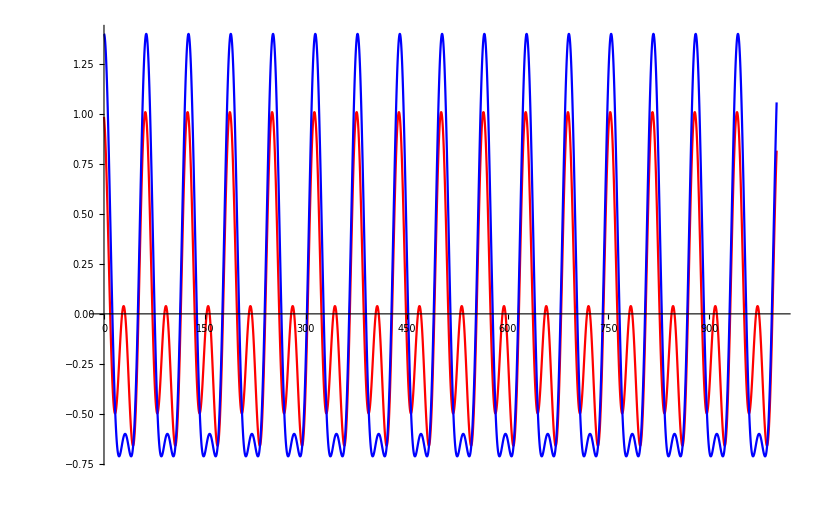

```mathematica
{ 0.5Cos[0.1 t]+0.5 Cos[0.2 t],0,   Sin[0.2 t] }.RotationMatrix[10.0 Degree ,{0,1,0}]
Plot[{%[[1]], Cos[0.1 t]+0.4 Cos[0.2 t] },{t,0,1000},PlotStyle->{Red, Blue}]
```

```mathematica
0.5Cos[0.19 t]+0.5 Cos[0.21 t]
```